```mathematica
data=Import["/home/mariana/Documentos/Ano_2/FC/Lab/Projeto3/g2p3c2_b/Temp_x.dat"];
```

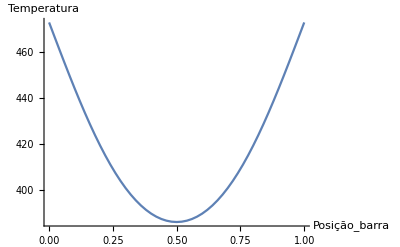

```mathematica
fig=ListLinePlot[data, AxesLabel->{Posição_barra, Temperatura}]
```

```mathematica
Export["/home/mariana/Documentos/Ano_2/FC/Lab/Projeto3/g2p3c2_b/TemP.pdf", fig, "PDF"]
```

/home/mariana/Documentos/Ano_2/FC/Lab/Projeto3/g2p3c2_b/TemP.pdf

```mathematica
?Export
```

Export[file.ext,expr] exports data to a file, converting it to the format corresponding to the file extension ext. 
Export[file,expr,format] exports data in the specified format.
Export[file,exprs,elems] exports data by treating exprs as elements specified by elems.